2. DOMAČA NALOGA

1. NALOGA

```mathematica
d = Daljica[{-1,1},{3,-1}]
d2 = Daljica[{-1, -1}, {3, 1}]
d3 = Daljica[{-1, 2}, {3, 0}]
```

Daljica[{-1,1},{3,-1}]

Daljica[{-1,-1},{3,1}]

Daljica[{-1,2},{3,0}]

1. pod naloga

```mathematica
Dolzina[Daljica[AA_, BB_]]:= Norm[BB - AA]
```

```mathematica
Dolzina[d]
```

2 √5

2. pod naloga

```mathematica
EnacbaNosilke[Daljica[AA_, BB_]]:=Module[{x1, y1, x2, y2, k, n},
{x1, y1}=AA;
{x2, y2}=BB;
k = (y2 - y1)/(x2-x1);
n = y1 - k *x1;
y ==  k x + n
]
```

```mathematica
EnacbaNosilke[d]
```

y==1/2-x/2

3. pod naloga

```mathematica
Slika[Daljica[AA_, BB_]]:= Line[{AA, BB}]
```

```mathematica
Slika[d]
```

Line[{{-1,1},{3,-1}}]

4. pod naloga

```mathematica
Narisi[d_Daljica]:=Graphics[Slika[d]]
Narisi[d__Daljica]:=Graphics[Map[Slika, List[d]]]
```

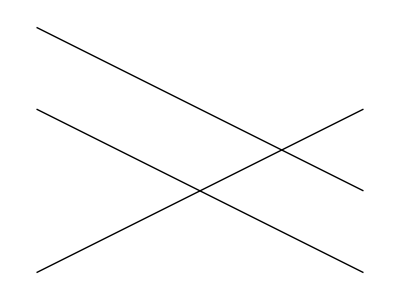

```mathematica
Narisi[d, d2, d3]
```

2. NALOGA

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]]:=Module[{resitev}, resitev = Solve[{AA + r * (BB - AA)== CC + s * (DD - CC), s ≥ 0, s≤ 1, r ≥ 0, r≤ 1},{s, r}]
]
```

```mathematica
Presek[d,d2]
```

{{s→1/2,r→1/2}}

```mathematica
Presek[d, d3]
```

{}

3. NALOGA

```mathematica
m1=Mnogokotnik[{0,0}, {1, 1}, {0,3}, {-1, 2}]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

1. pod naloga

```mathematica
Slika[Mnogokotnik[t__]]:=Line[{t}]
```

```mathematica
Slika[m1]
```

Line[{{0,0},{1,1},{0,3},{-1,2}}]

2. pod naloga

```mathematica
m1 = Append[m1, First[m1]]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}]

```mathematica
Narisi[m__Mnogokotnik]:= Graphics[Map[Slika, List[m]]]
```

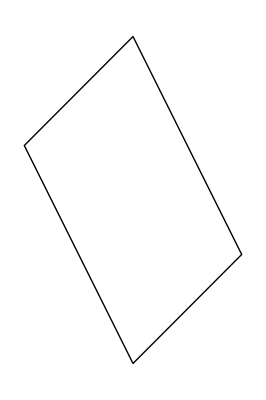

```mathematica
Narisi[m1]
```

APPEND, FIRST

```mathematica
?Append
```

Append[expr,elem] gives expr with elem appended. 
Append[elem] represents an operator form of Append that can be applied to an expression.

```mathematica
?First
```

First[expr] gives the first element in expr. 
First[expr,def] gives the first element if it exists, or def otherwise.

3. pod naloga

```mathematica
PravilniNKotnik[n_,r_]:=Graphics[{Line[Table[{r*Cos[(2 Pi*i)/n],r*Sin[(2 Pi*i)/n]},{i,0,n}]],Point[{0,0}]}]
```

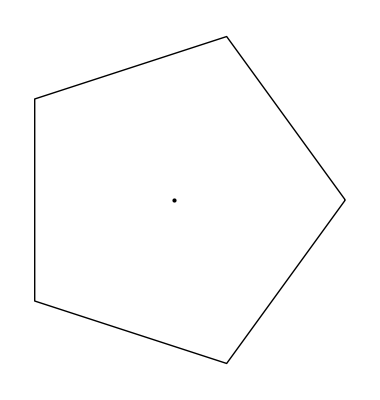

```mathematica
p5 = PravilniNKotnik[5,2]
```

4. pod naloga

```mathematica
PravilniNKotnik[n_, r_, phi_]:= Manipulate[Graphics[
{Line[Table[{r*Cos[(2Pi*i + x)/n],r*Sin[(2Pi*i + x)/n]},{i,0,n}]],Point[{0,0}]}], {x, 0, Pi}]
```

```mathematica
PravilniNKotnik[5, 2, Pi]
```

5. pod naloga

```mathematica
Daljice[Mnogokotnik[t__]]:=Partition[{t}, {2, 2}, 1]
```

```mathematica
m1
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}]

```mathematica
Daljice[m1]
```

{{{{0,0},{1,1}}},{{{1,1},{0,3}}},{{{0,3},{-1,2}}},{{{-1,2},{0,0}}}}

```mathematica
?Partition
Partition[{2, 1, 3,4,5}, 2]
Partition[{2, 1, 3,4,5}, 2,1]
```

Partition[list,n] partitions list into nonoverlapping sublists of length n. 
Partition[list,n,d] generates sublists with offset d. 
Partition[list,{n_1,n_2,…}] partitions a nested list into blocks of size n_1×n_2×….
Partition[list,{n_1,n_2,…},{d_1,d_2,…}] uses offset d_i at level i in list. 
Partition[list,n,d,{k_L,k_R}] specifies that the first element of list should appear at position k_L in the first sublist, and the last element of list should appear at or after position k_R in the last sublist. If additional elements are needed, Partition fills them in by treating list as cyclic. 
Partition[list,n,d,{k_L,k_R},x] pads if necessary by repeating the element x. 
Partition[list,n,d,{k_L,k_R},{x_1,x_2,…}] pads if necessary by cyclically repeating the elements x_i. 
Partition[list,n,d,{k_L,k_R},{}] uses no padding, and so can yield sublists of different lengths. 
Partition[list,nlist,dlist,{klist_L,klist_R},padlist] specifies alignments and padding in a nested list.

{{2,1},{3,4}}

{{2,1},{1,3},{3,4},{4,5}}

4. NALOGA

```mathematica
d = Daljica[{-1,1},{3,-1}];
d2 = Daljica[{-1,-1},{3,1}];
d3 = Daljica[{-1, 2},{3, 0}];
m1;
```

```mathematica
Presek[m_Mnogokotnik[AA_, BB_], d_Daljica[CC_,DD_]]:= Module[{a, b},
a = Daljice[m1];
b = d;
resitev = Solve[{AA + r * (BB - AA)== CC + s * (DD - CC), s ≥ 0, s≤ 1, r ≥ 0, r≤ 1}, {x, y}]]
```

```mathematica
Presek[m1, d]
```

Presek[Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}],Daljica[{-1,1},{3,-1}]]

```mathematica
Presek[m1, m2]
```

Presek[Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}],m2]

5. NALOGA

```mathematica
VsiPari[f_, sez1_, sez2_]:= Flatten[Outer[f, sez1, sez2], 1]
```

```mathematica
VsiPari[f, {1, 2,3 },{a, b}]
```

{f[1,a],f[1,b],f[2,a],f[2,b],f[3,a],f[3,b]}

1. pod naloga

```mathematica
?Outer
```

Outer[f,list_1,list_2,…] gives the generalized outer product of the list_i, forming all possible combinations of the lowest-level elements in each of them, and feeding them as arguments to f. 
Outer[f,list_1,list_2,…,n] treats as separate elements only sublists at level n in the list_i. 
Outer[f,list_1,list_2,…,n_1,n_2,…] treats as separate elements only sublists at level n_i in the corresponding list_i.

```mathematica
Outer[f, {1,2,3},{a,b}]
```

{{f[1,a],f[1,b]},{f[2,a],f[2,b]},{f[3,a],f[3,b]}}

```mathematica
Outer[{c,3},{4,3,{6}},{g,{f,h}},2]
```

{{{c,3}[4,g],{{c,3}[4,f],{c,3}[4,h]}},{{c,3}[3,g],{{c,3}[3,f],{c,3}[3,h]}},{{{c,3}[6,g],{{c,3}[6,f],{c,3}[6,h]}}}}

```mathematica
?Flatten
```

Flatten[list] flattens out nested lists. 
Flatten[list,n] flattens to level n. 
Flatten[list,n,h] flattens subexpressions with head h. 
Flatten[list,{{s_11,s_12,…},{s_21,s_22,…},…}] flattens list by combining all levels s_ij to make each level i in the result.

```mathematica
Flatten[{{b, 2},{1, 3, {4}},{f, {g, h}}}, 1]
```

{b,2,1,3,{4},f,{g,h}}

```mathematica
Flatten[[f, {1,2,3},{a,b}]]
```

Part::pkspec1: The expression f cannot be used as a part specification.

Flatten⟦f,{1,2,3},{a,b}⟧

2. pod naloga

```mathematica
m2 = Mnogokotnik[{0,0},{0,-1},{1,2},{-1, 2}]
m3 = Mnogokotnik[{0,1},{1,4},{2,3},{-5, 2}]
```

Mnogokotnik[{0,0},{0,-1},{1,2},{-1,2}]

Mnogokotnik[{0,1},{1,4},{2,3},{-5,2}]

```mathematica
Presek[m1_Mnogokotnik, m2_Mnogokotnik]:= VsiPari[f, m1, m2]
```

```mathematica
Presek[m1,m2]
```

Mnogokotnik[f[{0,0},{0,0}],f[{0,0},{0,-1}],f[{0,0},{1,2}],f[{0,0},{-1,2}],f[{1,1},{0,0}],f[{1,1},{0,-1}],f[{1,1},{1,2}],f[{1,1},{-1,2}],f[{0,3},{0,0}],f[{0,3},{0,-1}],f[{0,3},{1,2}],f[{0,3},{-1,2}],f[{-1,2},{0,0}],f[{-1,2},{0,-1}],f[{-1,2},{1,2}],f[{-1,2},{-1,2}],f[{0,0},{0,0}],f[{0,0},{0,-1}],f[{0,0},{1,2}],f[{0,0},{-1,2}]]

```mathematica
Presek[m1,m3]
```

Mnogokotnik[f[{0,0},{0,1}],f[{0,0},{1,4}],f[{0,0},{2,3}],f[{0,0},{-5,2}],f[{1,1},{0,1}],f[{1,1},{1,4}],f[{1,1},{2,3}],f[{1,1},{-5,2}],f[{0,3},{0,1}],f[{0,3},{1,4}],f[{0,3},{2,3}],f[{0,3},{-5,2}],f[{-1,2},{0,1}],f[{-1,2},{1,4}],f[{-1,2},{2,3}],f[{-1,2},{-5,2}],f[{0,0},{0,1}],f[{0,0},{1,4}],f[{0,0},{2,3}],f[{0,0},{-5,2}]]

6. NALOGA

Poišči enotski vektor, simetralo kota ter središče včrtanega kota v trikotniku z ogljišči A(2,3), B(-3,7), C(4,3).

```mathematica
EnotskiVektor[A_,B_]:=(B-A)/Razdalja[A,B]
```

```mathematica
EnotskiVektor[ {2,3},{-3,7}]
```

{-5/Razdalja[{2,3},{-3,7}],4/Razdalja[{2,3},{-3,7}]}

```mathematica
SimetralaK[B_,A_,C_]:=Premica[A,A+EnotskiVektor[A,B]+EnotskiVektor[A,C]]
```

```mathematica
SimetralaK[{2,3},{-3,7},{4,3}]
```

Premica[{-3,7},{-3+5/Razdalja[{-3,7},{2,3}]+7/Razdalja[{-3,7},{4,3}],7-4/Razdalja[{-3,7},{2,3}]-4/Razdalja[{-3,7},{4,3}]}]

```mathematica
SV[A_,B_,C_]:=Presek[SimetralaK[A,B,C],SimetralaK[B,C,A]]
```

```mathematica
SV[{2,3},{-3,7},{4,3}]
```

Presek[Premica[{-3,7},{-3+5/Razdalja[{-3,7},{2,3}]+7/Razdalja[{-3,7},{4,3}],7-4/Razdalja[{-3,7},{2,3}]-4/Razdalja[{-3,7},{4,3}]}],Premica[{4,3},{4-7/Razdalja[{4,3},{-3,7}]-2/Razdalja[{4,3},{2,3}],3+4/Razdalja[{4,3},{-3,7}]}]]